# Test: SubPixelFit library

Aims: 
1) create tests for (a) accuracy, (b) speed and (c) error handling 
2) Create testing cases:
	2.a) Symmetric gaussian particles + noise
	2.b) Non-symmetric gaussian particles + noise
	2.c) Real practice images (500nm) particles
	2.d) Special cases with possible errors

Specifications:

## Tracking function

input: image with background substracted
output: {x,y, confidence, size (optional), angle (optional), flattening(optional)}

# Versions
 - 2015-03-09 - Last use to calibrate for multiple particles
 - 2015-12-15 - Assesed accuracy of subpixel tracking

## Laoding Tools

```mathematica
(*get key library - namy parts of this code might need to be overwritten for testing*)
Import @ FileNameJoin@{DirectoryName[NotebookDirectory[] ], "bin/packages/SubPixelFit.m"}
```

```mathematica
<< SubPixelFit`
```

#### Generate testing data set (2.a)

```mathematica
GenerateGaussianParticle[box_, μ_, size_:10.0, θ_:0, flattening_:0, noise_:0.03] := 
Block[{data,a,b,c, σx,σy, dist, x,y,var},
σx = size √(1-flattening); (*preserve area of 'size' particle*)
σy = size/√(1-flattening);
a = Cos[θ]^2/(2 σx^2) + Sin[θ]^2/(2 σy^2) //N;
b= (-Sin[2θ])/(4 σx^2) + Sin[2θ]/(4 σy^2)//N;
c = Sin[θ]^2/(2 σx^2) + Cos[θ]^2/(2 σy^2)//N;
var = Inverse@{{a,b},{b,c}};
dist = 2π Det[var]^(1/2)  PDF[ MultinormalDistribution[Reverse@μ+{0.5,0.5}, var],{x,y}];
data = Round[  255 Table[ dist, {x,1,box}, {y,1,box}] ];
(*Print["σx"-> σx];
Print["matrix"->  {{a,b},{b,c}}];
Print["dist"->  dist//Simplify];*)
(ImageReflect@Image[data, "Byte"]) ~ ImageEffect ~ {"GaussianNoise",noise}
]
```

```mathematica
Manipulate[Show[GenerateGaussianParticle[20,{x,y}, size, angle, flt, 0.02], ImageSize-> Small], {angle, 0, Pi}, {{size,2}, 0.2, 4}, {{x,10},-10,30}, {{y,10},0,20}, {{flt,0.5},0,0.9}]
```

Show::gtype: GenerateGaussianParticle is not a type of graphics.

```mathematica
(*output: list of {image, position, size, angle, flattening}*)
GenerateTestDataSet[n_, box_, sizeRange_, flatteningRange_:{0,0}, noise_]:= Module[
{results,posRange, randomPos},
posRange[size_] := {0, box} + {1,-1} * 1.5 size;
randomPos[posRange_] := {RandomReal@posRange, RandomReal@posRange};
results =  Table[{{}, {}, RandomReal@sizeRange, RandomReal@{0, Pi},RandomReal@flatteningRange} , {i, n}];
results⟦All, 2⟧ = randomPos/@posRange /@ results⟦All, 3⟧;
results⟦All, 1⟧ = GenerateGaussianParticle[box, #⟦2⟧, #⟦3⟧, #⟦4⟧, #⟦5⟧,noise] &/@ results;
results
]
```

```mathematica
(*output: list of {image, position, size, angle, flattening}*)
GenerateTestDataSetOnAxis[n_, box_, sizeRange_, flatteningRange_:{0,0}]:= Module[
{results,posRange, randomPos},
posRange[size_] := {0, box} + {1,-1} * 1.5 size;
randomPos[posRange_] := {RandomReal@posRange, Mean@posRange};
results =  Table[{{}, {}, RandomReal@sizeRange, RandomReal@{0, Pi},RandomReal@flatteningRange} , {i, n}];
results⟦All, 2⟧ = randomPos/@posRange /@ results⟦All, 3⟧;
results⟦All, 1⟧ = GenerateGaussianParticle[box, #⟦2⟧,#⟦3⟧, #⟦4⟧, #⟦5⟧] &/@ results;
results
]
```

```mathematica
(*multiple images close by*)
GenerateTestDataSetTwoParticles[n_, box_, sizeRange_, flatteningRange_, separationRange_]:= 
Module[ {results, posRange, randomPos, secondPos, secondParticle},
posRange[size_] := {0, box} + {1,-1} * 1.8 size;
randomPos[posRange_] := {RandomReal@posRange, RandomReal@posRange};
results =  Table[{{}, {}, RandomReal@sizeRange, RandomReal@{0, Pi},RandomReal@flatteningRange} , {i, n}];
results⟦All, 2⟧ = randomPos /@ posRange /@ results⟦All, 3⟧;
results⟦All, 1⟧ = GenerateGaussianParticle[box, #⟦2⟧,#⟦3⟧, #⟦4⟧, #⟦5⟧] &/@ results;
(*generate another image for second partile*)
secondPos[fisrtPos_] := fisrtPos + RandomReal[ separationRange ]*{Cos[#], Sin[#]} &@RandomReal[{0,2 Pi}];
secondParticle = GenerateGaussianParticle[box, #, Mean@sizeRange, 0,0] &/@ (secondPos /@ results⟦All, 2⟧);
results⟦All, 1⟧ = MapThread[ ImageAdd,  { results⟦All, 1⟧, secondParticle} ];
results
]
```

#### Assesment tools

Want to know:
1) time it took the function
2) Accuracy in X fit
3) Accuracy in Y fit
4) Drop rate (accuracy paramter <0.75)
5) Size estimate - relative is enough, check how linear it is (correlation coefficient?) 
6) angle - range {0, π} 
7) flattening - relative is enough

Estimator should include typical error, but penalise large errors thus something along the lines of √⟨(X - μ)^2⟩

```mathematica
(*return all results as listed above*)
AssesFunction[name_,fn_, testSet_]:= Module[
{foundSet, time,accuracyPos, correlationSize, accuracyAngle, correlationFlattening, dropRate},

{time, foundSet} = AbsoluteTiming[ fn/@ testSet⟦All, 1⟧ ];
accuracyPos =  Sqrt@Mean@Transpose@((foundSet⟦All, {1,2}⟧ - testSet⟦All, 2⟧)^2);
(*alternative*)
(*accuracyPos =  Mean@Abs@Transpose@(foundSet⟦All, {1,2}⟧ - dataSet⟦All, 2⟧);*)
dropRate = N[ Count[foundSet⟦All, 3⟧,_?(#<0.75&)] / Length@testSet];
correlationSize = If[ Length@First@foundSet <4, "-",
Correlation[testSet⟦All, 3⟧, foundSet⟦All, 4⟧]    ];
accuracyAngle = If[ Length@First@foundSet <5, "-",
180.0/Pi *Mean@((Min@Abs@{#, #-Pi}&)/@(testSet⟦All, 4⟧- foundSet⟦All, 5⟧)) ];
correlationFlattening = If[ Length@First@foundSet <6, "-",
Correlation[testSet⟦All, 5⟧, foundSet⟦All, 6⟧]    ];
<|"Name"-> name,
"Time"->  time, 
"√⟨SuperscriptBox[Δx, 2]⟩"-> accuracyPos⟦1⟧,
 "√⟨SuperscriptBox[Δy, 2]⟩"-> accuracyPos⟦2⟧,
"Drop Rate" -> dropRate,
"ρ(size)"-> correlationSize, 
"⟨|Δα|⟩"-> accuracyAngle,
"ρ(f)"-> correlationFlattening|>
]
```

## Generate training sets

#### Gaussian Particles (esay)

```mathematica
testSet = GenerateTestDataSet[30000, 8, {1.,1.1}, {0.05,0.08},0.004];
testSet⟦;;10, 1⟧
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Data on axis

```mathematica
testSet = GenerateTestDataSetOnAxis[30000, 8, {1.2,1.5}, {0.05,0.08}];
testSet⟦;;10, 1⟧
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Real images (todo)

#### Multiple particles (todo)

```mathematica
testSet =GenerateTestDataSetTwoParticles[500, 9, {1.6,1.7},{0.05,0.08}, {6,8.5}];
testSet⟦;;20, 1⟧
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Run Test

```mathematica
Dataset[{
(*AssesFunction["Centroid (built in)", Centroid, testSet],*)
(*AssesFunction["CentroidCustom", CentroidCustom, testSet],*)
(*AssesFunction["SPFCentroidWithProperties", SPFCentroidWithProperties, testSet],*)
(*AssesFunction["SPFCentroidWithProperties2", SPFCentroidWithProperties2, testSet],*)
(*AssesFunction["SPFGaussian", SPFGaussian, testSet],*)
AssesFunction["SPFGaussianOptimised", SPFGaussianOptimised, testSet],
(*AssesFunction["SPFGaussianVarianceMatrix", SPFGaussianVarianceMatrix, testSet],*)
(*AssesFunction["SPFGaussianFixedAngle", SPFGaussianFixedAngle, testSet],*)
AssesFunction["SPFGaussianFixed",SPFGaussianFixed, testSet]
(*AssesFunction["SubPixel2DGaussianFixedFit (old)", SubPixel2DGaussianFixedFit, testSet]*)
}]
```

$Aborted[]

#### Noise and fitting error

Run on 2015-12-22
Gaussian particle paramters: GenerateTestDataSet[10000, 8, {1.,1.1}, {0.05,0.08}, noise]
Testing routine: “SPFGaussianOptimised”
Noise type: “GaussianNoise” - adds zero-mean Gaussian noise with standard deviation σ (the parameter)
Tested with 10000 particles

```mathematica
{time, foundSet} = AbsoluteTiming[ SPFGaussianOptimised/@ testSet⟦All, 1⟧ ]; 
accuracy = Mean@Sqrt@Mean@Transpose@((foundSet⟦All, {1,2}⟧ - testSet⟦All, 2⟧)^2)
"time" -> time
```

0.00326351

time→89.4432

```mathematica
errorDependance = {{"noise", "subpixel accuracy", "sample image"},
{0. , 0.0008627646290243423,-Graphics-},
{0.001,0.0010792466333627508 , -Graphics-},
{0.003,0.002581050045527386 , -Graphics-},
{0.004, 0.0032635127298899272,-Graphics-},
{0.005, 0.003938221530491238, -Graphics-},
{0.01, 0.007676378737570633, -Graphics-},
{0.02,0.015162132003315199, -Graphics-},
{0.03,0.022790304627624904 , -Graphics-},
{0.04, 0.030573928543475522,-Graphics-},
{0.05,0.03813245606305967, -Graphics-},
{0.1, 0.07846842127458675, -Graphics-},
{0.15,0.12174701234558617 ,-Graphics-},
{0.2,0.17526096102624877,-Graphics-}
};
```

FittedModel[-0.00147489+0.849445 x]

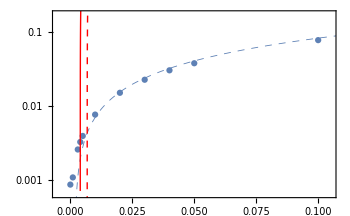

```mathematica
fit = LinearModelFit[errorDependance⟦2;;,{1,2}⟧,x,x ]
expNoise = 0.004;

fig = Show[
ListLogPlot[
errorDependance⟦2;;,{1,2}⟧ ,
PlotRange->{{-0.005,0.105},Automatic}
],
LogPlot[fit[noise ], {noise, 0, 0.2}, 
PlotRange->All, PlotStyle->Directive[ AbsoluteThickness[0.6], Dashed]
],
(*show experimental noise from iScat setup*)
LogPlot[1000(noise-expNoise) , {noise, 0, 0.05}, 
PlotRange->All, PlotStyle->Directive[ AbsoluteThickness[1], Red]
],
(*show experimental noise from iScat setup*)
LogPlot[1000(noise-0.0068) , {noise, 0, 0.05}, 
PlotRange->All, PlotStyle->Directive[ AbsoluteThickness[1], Red, Dashed]
],
Frame-> True,
FrameStyle->Directive[GrayLevel[0],12,FontFamily->"Helvetica",AbsoluteThickness[1.]],
ImageSize->350
]
```

```mathematica
Rasterize@Show[errorDependance⟦10,3⟧, ImageSize->Tiny]
```

-Graphics-

```mathematica
KPlotsTheme
```

{Frame→True,FrameStyle→Directive[GrayLevel[0],12,FontFamily→Helvetica Neue,AbsoluteThickness[1.]],FrameTicks→{{LinTicks,LinTicks[#1,#2,ShowTickLabels→False]&},{LinTicks,LinTicks[#1,#2,ShowTickLabels→False]&}},GridLines→None,ImageSize→350}

#### Look at detailed deviations

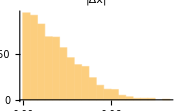
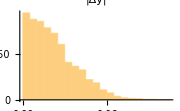

```mathematica
method = (SPFGaussianOptimised@#&);
foundSet = method/@ testSet⟦All, 1⟧ ; 
dPos = Abs@(foundSet⟦All, {1,2}⟧ - testSet⟦All, 2⟧);
Row@{Histogram[dPos⟦All,1⟧, ImageSize->Small, PlotLabel->"|Δx|"], Histogram[dPos⟦All,2⟧, ImageSize->Small, PlotLabel->"|Δy|"]}
```

```mathematica
method = (SPFGaussianOptimised@#&);
foundSet = method/@ testSet⟦All, 1⟧ ; 
dPos = (foundSet⟦All, {1,2}⟧ - testSet⟦All, 2⟧);
"Mean" -> Mean[dPos]
```

Mean→{0.0000146977,6.42099×10^-6}

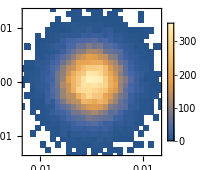

```mathematica
ticks = {-0.01,0.,0.01};
DensityHistogram[dPos,{30,30}, 
(*FrameLabel->{"Δx","Δy"},*)
PlotRange->{{-0.013,0.013},{-0.013,0.013}},
ImageSize-> 170,FrameTicks->{{LinTicks[ticks],LinTicks[ticks,ShowTickLabels->False]&},{LinTicks[ticks],LinTicks[ticks,ShowTickLabels->False]&}},
ChartLegends->Placed[Automatic,Right],
KPlotsTheme
]
```

```mathematica
BarLegend[Automatic,{0,1}]
```

BarLegend[Automatic,{0,1}]

```mathematica
KPlotsTheme
```

{Frame→True,FrameStyle→Directive[GrayLevel[0],12,FontFamily→Helvetica Neue,AbsoluteThickness[1.]],FrameTicks→{{LinTicks,LinTicks[#1,#2,ShowTickLabels→False]&},{LinTicks,LinTicks[#1,#2,ShowTickLabels→False]&}},GridLines→None,ImageSize→350}

```mathematica
DistributionFitTest[dPos]
```

0.0061818

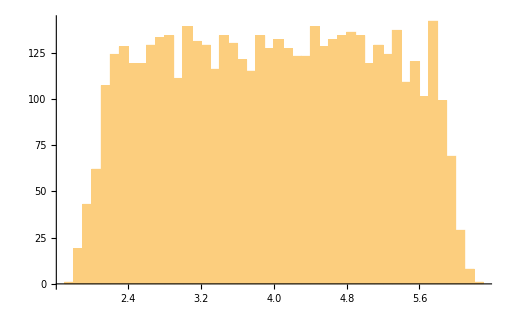

```mathematica
Histogram[foundSet⟦All, 1⟧, 60 ]
```

```mathematica
FindDistribution[dPos⟦;;,1⟧]
```

StudentTDistribution[0.000282425,0.0260905,40.9798]

#### Error Statistical Properies

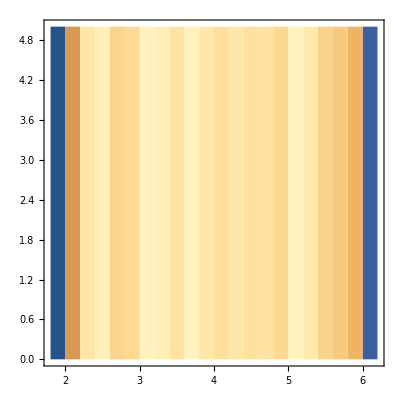

```mathematica
DensityHistogram[testSet⟦All,2⟧]
```

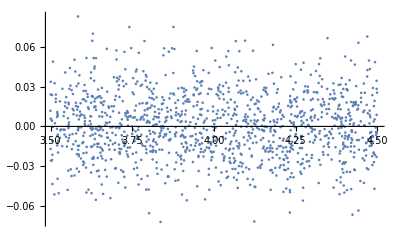

-0.0378503

```mathematica
lists = Select[
Transpose[ {testSet⟦All,2,1⟧, dPos⟦All,1⟧}],
3.5<#⟦1⟧<4.5& 
];
ListPlot[lists]
Correlation[lists⟦All,1⟧, lists⟦All,2⟧]
```

```mathematica
correlationOfErrors[range_List, elem_List] := Block[
{},
lists = Select[
Transpose[ {testSet⟦All,2,elem⟦1⟧⟧, dPos⟦All,elem⟦2⟧⟧}],
range⟦1⟧<#⟦1⟧<range⟦2⟧& 
];
Correlation[lists⟦All,1⟧, lists⟦All,2⟧]
]
```

```mathematica
Partition[
correlationOfErrors[{3.6,4.4}, #]&/@Tuples[{1,2},2],
2 ]
```

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

(-0.0479489 | -0.0258769
Correlation[{4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4942,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.},1] | 1)
 |  |  |  |

```mathematica
xAndErrors = Transpose@{testSet⟦All,2,1⟧,dPos};
```

```mathematica
(*select within one pixel *)
xAndErrors = Select[xAndErrors, 3.5<#⟦1⟧<4.5&];
```

```mathematica
perm = Permutations[xAndErrors, {2}];
```

```mathematica
processPerms[{p1_,p2_}]:= {p1⟦1⟧-p2⟦1⟧, p1⟦2,1⟧, p1⟦2,2⟧,p2⟦2,1⟧, p2⟦2,2⟧};
```

```mathematica
distances = processPerms/@perm;
```

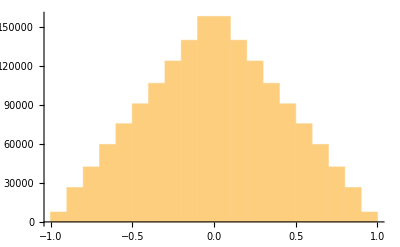

```mathematica
distances⟦All,1⟧//Histogram
```

```mathematica
corrVsDistance[dx_]:= Correlation @@ Transpose[  Select[distances, dx<Abs[#⟦1⟧]<dx+ 0.1&]⟦All,{2,3}⟧  ]
```

```mathematica
corrVsDistance/@Range[0,0.9,0.1]
```

{-0.0075539,-0.0102401,-0.00997915,-0.0194925,-0.0184119,0.00793406,0.016351,0.00217338,0.0125242,0.0344256}

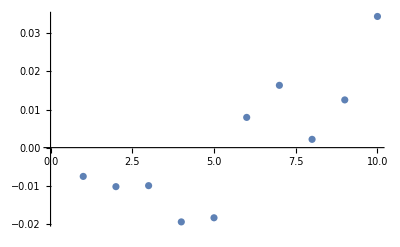

```mathematica
ListPlot[%]
```

#### Test if errors are correlated based on distance

Generate 1D dataset

#### Something else

```mathematica
angles = Transpose@{ testSet⟦All,4⟧, foundSet⟦All,5⟧}*180/Pi;
```

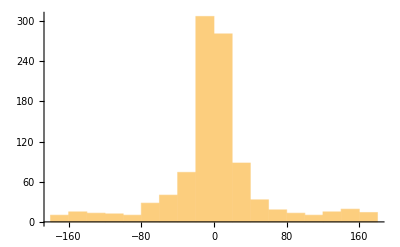

```mathematica
Histogram[ (angles⟦All,1⟧ - angles⟦All,2⟧)]
```

```mathematica
angles⟦;;20⟧
```

#### Overlay point of detection

```mathematica
ShowPosOverlayed[testRow_,fn_]:=Block[{pos, img = testRow⟦1⟧},
pos = (fn@img)⟦{1,2}⟧;
Print["pos" -> pos];
Show[img,Graphics@Flatten@{Green,Point[testRow⟦2⟧],Red,Point[pos]}, ImageSize -> Small]
]
```

pos→{1.98322,2.47979}

pos→{2.60958,4.4582}

pos→{4.78019,2.35894}

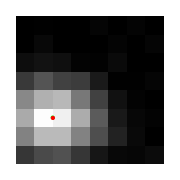
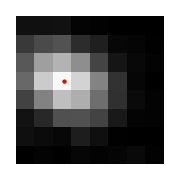
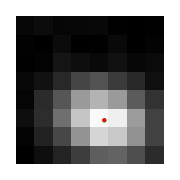

```mathematica
ShowPosOverlayed[#, SPFGaussian]&/@testSet⟦;;3⟧
```